## Functions

### Binary Functions

```mathematica
PartitionAt[list_,lengths_]:=Block[{},
totallengths=Transpose[{Drop[FoldList[Plus,1,lengths],-1],Rest[FoldList[Plus,0,lengths]]}];
If[Fold[Plus,0,lengths]=!=Length[list],AppendTo[totallengths,Length[list]-Fold[Plus,0,lengths]]];
list⟦Range[Sequence@@#]⟧&/@totallengths
]
```

```mathematica
BinToGray[bin_]:=Block[{a,b,c,gray,binary},
gray={};binary=bin;
b=First[binary];
AppendTo[gray,b];
binary=Rest[binary];
(a=#;
AppendTo[gray,If[b===a,0,1]];
b=a;
)&/@binary;
gray]
```

```mathematica
GrayToBin[gra_]:=Block[{a,b,c,gray,binary},
gray=Rest[gra];
binary={};
a=First[gra];
AppendTo[binary,First[gra]];
(If[#===1&&a===1,AppendTo[binary,0];a=0,If[#===1&&a===0,AppendTo[binary,1];a=1,AppendTo[binary,a]]]&/@gray);
binary
]
```

```mathematica
RandomUnion[no_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{no}]]
```

```mathematica
RandomUnion[no_,subno_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{subno}]]
```

```mathematica
CreateChrom[number_,length_Integer,numbers_Integer]:=Table[IntegerDigits[RandomInteger[{0,2^(length numbers)-1}],2,length numbers],{number}]
```

```mathematica
CreateChrom[number_,length_List,numbers_Integer]:=Table[IntegerDigits[RandomInteger[{0,2^(Plus@@length)-1}],2,Plus@@length numbers],{number}]
```

```mathematica
TurnToBin[list_List,length_Integer,number_Integer,start_Integer|start_Real,end_Integer|end_Real]:=Flatten[Block[{a=#},PadLeft[RealDigits[Ordering[Abs[list⟦a⟧-#]]⟦1⟧-1,2]⟦1⟧,length,0]&[Range[start,end,(end-start)/(2^length-1)]]]&/@Range[number]]
```

```mathematica
TurnToBin[list_List,length_Integer,number_Integer,start_List,end_Integer|end_Real]:=Flatten[Block[{a=#},PadLeft[RealDigits[Ordering[Abs[list⟦a⟧-#]]⟦1⟧-1,2]⟦1⟧,length,0]&[Range[start⟦a⟧,end,(end-start⟦a⟧)/(2^length-1)]]]&/@Range[number]]
```

```mathematica
TurnToBin[list_List,length_Integer,number_Integer,start_Integer|start_Real,end_List]:=Flatten[Block[{a=#},PadLeft[RealDigits[Ordering[Abs[list⟦a⟧-#]]⟦1⟧-1,2]⟦1⟧,length,0]&[Range[start,end⟦a⟧,(end⟦a⟧-start)/(2^length-1)]]]&/@Range[number]]
```

```mathematica
TurnToBin[list_List,length_Integer,number_Integer,start_List,end_List]:=Flatten[Block[{a=#},PadLeft[RealDigits[Ordering[Abs[list⟦a⟧-#]]⟦1⟧-1,2]⟦1⟧,length,0]&[Range[start⟦a⟧,end⟦a⟧,(end⟦a⟧-start⟦a⟧)/(2^length-1)]]]&/@Range[number]]
```

```mathematica
TurnToRange[binnumber_,length_Integer,number_Integer,start_Integer,range_Integer]:=(N[start+(FromDigits[Take[binnumber,{#,#+(length)-1}],2]*((range-start)/(2^(length)-1)))]&/@Range[1,length*number,(length)])
```

```mathematica
TurnToRange[binnumber_,length_Integer,number_Integer,start_List,range_Integer]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1⟧,#⟦1⟧+(length)-1}],2]*((range-#⟦2⟧)/(2^(length)-1)))]&/@MapThread[List,{Range[1,length*number,(length/number)],start}])
```

```mathematica
TurnToRange[binnumber_,length_Integer,number_Integer,start_Integer,range_List]:=(N[start+(FromDigits[Take[binnumber,{#⟦1⟧,#⟦1⟧+(length)-1}],2]*((#⟦2⟧-start)/(2^(length/number)-1)))]&/@MapThread[List,{Range[1,length*number,(length/number)],range}])
```

```mathematica
TurnToRange[binnumber_,length_Integer,number_Integer,start_List,range_List]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1⟧,#⟦1⟧+(length)-1}],2]*((#⟦3⟧-#⟦2⟧)/(2^(length)-1)))]&/@MapThread[List,{Range[1,length*number,length],start,range}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_Integer,start_Integer,range_Integer]:=(N[start+(FromDigits[Take[binnumber,{#⟦1⟧,#⟦1⟧+#⟦2⟧-1}],2]*((range-start)/(2^(#⟦2⟧)-1)))]&/@MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_Integer,start_List,range_Integer]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((range-#⟦2⟧)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],start}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_Integer,start_Integer,range_List]:=(N[start+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((#⟦2⟧-start)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],range}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_Integer,start_List,range_List]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((#⟦3⟧-#⟦2⟧)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],start,range}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_List,start_Integer,range_Integer]:=(N[start+(FromDigits[Take[binnumber,{#⟦1⟧,#⟦1⟧+#⟦2⟧-1}],2]*((range-start)/(2^(#⟦2⟧)-1)))]&/@MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_List,start_List,range_Integer]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((range-#⟦2⟧)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],start}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_List,start_Integer,range_List]:=(N[start+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((#⟦2⟧-start)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],range}])
```

```mathematica
TurnToRange[binnumber_,length_List,number_List,start_List,range_List]:=(N[#⟦2⟧+(FromDigits[Take[binnumber,{#⟦1,1⟧,#⟦1,1⟧+#⟦1,2⟧-1}],2]*((#⟦3⟧-#⟦2⟧)/(2^(#⟦1,2⟧)-1)))]&/@MapThread[List,{MapThread[List,{Drop[FoldList[Plus,1,length],-1],length}],start,range}])
```

```mathematica
FitnessAll[list_,length_,number_,start_,range_,rawdata_,fitdata_]:=(FitnessValue[TurnToRange[#,length,number,start,range]]&/@list)
```

```mathematica
FitnessAll[list_,length_,number_,start_,range_,rawdata_,fitdata_]:=Block[{fitlist={},fitans,finalfitlist},
If[$parallel,
finalfitlist=MapIndexed[If[Position[Most[rawdata],#]=!={},fitdata⟦Sequence@@Position[Most[rawdata],#]⟦1⟧⟧,AppendTo[fitlist,{#,#2⟦1⟧}];Null]&,(TurnToRange[#,length,number,start,range]&/@list)];
fitans=FitnessValue[fitlist⟦All,1⟧];
finalfitlist=ReplacePart[finalfitlist,MapIndexed[Rule[fitlist⟦#2⟦1⟧,2⟧,#]&,fitans]];
finalfitlist,
DistributeDefinitions[FitnessValue];
ParallelMap[If[Position[Most[rawdata],#]=!={},fitdata⟦Sequence@@Position[Most[rawdata],#]⟦1⟧⟧,FitnessValue[#]]&,(TurnToRange[#,length,number,start,range]&/@list)]
]
]
```

```mathematica
CumulativeProbabilities[list_,length_,number_,start_,range_,rawdata_,fitdata2_]:=Block[{a},
a=FitnessAll[list,length,number,start,range,rawdata,fitdata2];
fitdata={Sequence@@fitdata,a};
Rest[FoldList[Plus,0,a/Total[a]]]
]
```

```mathematica
randomnumbers[number_]:=(SeedRandom[];RandomReal[{0,1},number])
```

```mathematica
selectionmethods={Global`Roulette,Global`Universal,Global`Truncation,Global`Tournament,Global`Different}
```

```mathematica
SelectionRoulette[list_,probab_,number_,opts___]:=Block[{a,random=randomnumbers[number]},
list⟦breedinglist=(a=#;
Length[Select[probab,#<a&]]+1)&/@random⟧]
```

```mathematica
SelectionDifferent[list_,probab_,number_,opts___]:=Block[{a,probabs},
probabs=Prepend[probab⟦#⟧-probab⟦#-1⟧&/@Range[2,Length[probab]],First[probab]];
a=Length[list]-Range[number]+1;
list⟦breedinglist=Ordering[probabs]⟦a⟧⟧
]
```

```mathematica
SelectionUniversal[list_,probab_,number_,opts___]:=Block[{a,linear=Range[1/number,1,1/number]},list⟦breedinglist=((a=#1;Length[Select[probab,#1<a&]]+1)&)/@linear⟧]
```

```mathematica
SelectionTruncation[list_,probab_,number_,opts___]:=Block[{a,b,threshold,c},
threshold=Global`TruncationThreshold/.{opts}/.{Global`TruncationThreshold->0.5};
If[printedsetting=!=True,Print["Using TruncationThreshold → "<>ToString[threshold]];printedsetting=True];
a=MapThread[Subtract,{probab,Prepend[Most[probab],0]}];
b=Sort[Transpose[{a,list}],#1⟦1⟧<#2⟦1⟧&];
c=Take[b,-Round[threshold Length[list]]];
breedinglist=(Position[list,#1]⟦1,1⟧&)/@c⟦All,2⟧;c⟦All,2⟧⟦RandomInteger[{1,Length[c]},Length[c]]⟧]
```

```mathematica
SelectionTournament[list_,probab_,number_,opts___]:=Block[{a=MapThread[Subtract,{probab,Prepend[Most[probab],0]}],b=a,tour},
tour=Global`TournamentNumber/.{opts}/.{Global`TournamentNumber->Ceiling[number/5]};
If[printedsetting=!=True,Print["Using TournamentNumber → "<>ToString[tour]];printedsetting=True];Table[((a=ReplacePart[a,0,#1];AppendTo[breedinglist,#1];list⟦#1⟧)&)[(Position[a,Max[#1]]⟦1,1⟧&)[a⟦RandomUnion[number,tour]⟧]],{number}]]
```

```mathematica
bin6[b_,c_]:=b[[#]]&/@Split[Ordering[c],c[[#1]]==c[[#2]]&];
```

```mathematica
Clear[SelectforCrossover]
```

```mathematica
SelectforCrossover[list_,numbers_:5,pc_:0.25]:=Block[{a,positionsofcross,randompos,breeding,notbreeding},
randompos=RandomUnion[numbers];
a=#<pc&/@randomnumbers[numbers];
breeding:=Position[a,True]⟦All,1⟧;
notbreeding:=Position[a,False]⟦All,1⟧;
If[OddQ[Length[breeding]],
If[RandomInteger[{1,2}]===1||Length[breeding]===Length[a],
a=ReplacePart[a,breeding⟦RandomInteger[{1,Length[breeding]}]⟧->False];,
a=ReplacePart[a,notbreeding⟦RandomInteger[{1,Length[notbreeding]}]⟧->True];
];
];
positionsofcross=Transpose[{randompos,a}];
crossoverlist=positionsofcross;
(list⟦#⟦1⟧⟧&)/@positionsofcross]
```

```mathematica
Crossover[datalistin_,crosslist_,length_,numbers_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata},
If[Head[length]===List,lengths=Plus@@length,lengths=length numbers];
crossingpositions=Select[crosslist,#⟦2⟧===True&]⟦All,1⟧;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
crosseddata=Partition[
Flatten[
bin6[
Partition[
Flatten[
Block[{list=datalist⟦#⟧,pos,c1last,c2last,c1new,c2new},
((pos=RandomInteger[{1,lengths}];c1last=Take[list⟦1⟧,-(lengths-pos)];c2last=Take[list⟦2⟧,-(lengths-pos)];c1new=Flatten[Append[Take[list⟦1⟧,pos],c2last]];c2new=Flatten[Append[Take[list⟦2⟧,pos],c1last]];{c1new,c2new}))]&/@pairedcrossingpositions],lengths],randomcrossingpositions]],lengths];
(datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@Transpose[{crossingpositions,crosseddata}];datalist]
```

```mathematica
reinsertionmethods={Global`Elitist,Global`Uniform,Global`Pure,Global`Fitness}
```

```mathematica
ReinsertPure[olddata_,newdata_,positions_,jds___]:=Block[{a=RandomUnion[Length[positions]]},
newdata⟦a⟧
]
```

```mathematica
ReinsertFitness[olddata_,newdata_,null_,genelength_,nogenes_,start_,end_]/;Length[newdata]≥Length[olddata]:=Block[{a,random=RandomUnion[Length[olddata]],bnewdata=GrayToBin[#]&/@newdata,fitdata2,positions},
a=olddata;
fitdata2=FitnessValue[TurnToRange[#,genelength,nogenes,start,end]]&/@bnewdata;
(*Print["Fitdata offspring = ",fitdata2];
Print["Fitdata ordered = ",Ordering[fitdata2,-Length[olddata]]];*)
positions=Ordering[fitdata2,-Length[olddata]];
(a=ReplacePart[a,#⟦1⟧->#⟦2⟧])&/@Transpose[{random,newdata⟦positions⟧}];a]
```

```mathematica
ReinsertFitness[olddata_,newdata_,positions_,genelength_,nogenes_,start_,end_]/;Length[newdata]<Length[olddata]:=
(Print["Not enough offspring, using Reinsertion Method → Elitist"];
ReinsertElitist[olddata,newdata])
```

```mathematica
ReinsertUniform[olddata_,newdata_,Null___]:=Block[{a,positions=RandomUnion[Length[olddata],Length[newdata]]},
(*Print["Uniform Positions = ",positions];*)
a=olddata;
(a=ReplacePart[a,#⟦2⟧,#⟦1⟧])&/@Transpose[{positions,newdata}];
a]
```

```mathematica
ReinsertElitist[olddata_,newdata_,Null___]:=Block[{a,random=RandomUnion[Length[newdata]],positions},
a=olddata;
positions=Ordering[fitdata⟦-1⟧]⟦Range[Length[newdata]]⟧⟦random⟧;
(a=ReplacePart[a,#⟦1⟧->#⟦2⟧])&/@Transpose[{positions,newdata}];a]
```

```mathematica
Mutate[list_,lengths_,numbers_,mr_]:=Block[{a,b,number},If[Head[lengths]===List,number=Plus@@lengths,number=lengths numbers];
a=Flatten[list];
b=Flatten[Position[RandomReal[{0,1},Length[Flatten[a]]],_?(#1<mr&)]];
(If[a⟦#1⟧===1,a=ReplacePart[a,#1->0],a=ReplacePart[a,#1->1]]&)/@b;Partition[a,number]]
```

### NDSGA Functions

```mathematica
ClearDominates[]:=Block[{},
DownValues[Dominates]={};
Dominates[p_,q_,m_]:=Dominates[p,q,m]=Block[{pans,qans},
pans=#[p]&/@m;
qans=#[q]&/@m;
And@@{Or@@(#⟦1⟧<#⟦2⟧&/@Transpose[{pans,qans}]),
And@@(#⟦1⟧≤#⟦2⟧&/@Transpose[{pans,qans}])}
]
];
ClearDominates[];
```

```mathematica
ClearDominates[]:=Block[{},
DownValues[Dominates]={};
Dominates[p_,q_,m_]:=Dominates[p,q,m]=Block[{pans,qans},
pans=#[p]&/@m;
qans=#[q]&/@m;
And@@(#⟦1⟧≤#⟦2⟧&/@Transpose[{pans,qans}])
]
];
ClearDominates[];
```

```mathematica
Clear[FastNonDominatedSort];
FastNonDominatedSort[Pin_,m_]:=Block[{F,n,H,i,S},
F[1]={};
Map[Block[{p=#},
Map[Block[{q=#},
n[p]=0;
If[Dominates[p,q,m],
AppendTo[S[p],q],
If[Dominates[q,p,m],
n[p]=n[p]+1;
]];
]&,Pin];
If[n[p]==0,
AppendTo[F[1],p]
];
]&,Pin];
i=1;
While[Length[F[i]]>0,
H={};
Map[Block[{p=#},
Map[Block[{q=#},
n[q]=n[q]-1;
If[n[q]==0,
AppendTo[H,q]];
]&,S[p]]
]&,F[i]];
i++;
F[i]=H;
];
F[#]&/@Range[i-1]
]
```

```mathematica
CrowdingDistanceAssignment[Iin_,m_]:=Module[{Isorted,l,I,Iorder},
I=Iin;
l=Length[I];
Set[Idistance[#],0]&/@Range[l];
Map[Block[{n=#},
Iorder=Ordering[I,All,n[#1]<n[#2]&];
Idistance[Iorder⟦1⟧]=Idistance[Iorder⟦-1⟧]=∞;
(*Idistance[0]=Idistance[l]=∞;*)
Map[Block[{i=#},
Idistance[i]=Idistance[i]+(n[I⟦Iorder⟦i+1⟧⟧]-n[I⟦Iorder⟦i-1⟧⟧])^2;
]&,Range[2,l-1]];
]&,m];
Idistance[#]&/@Range[l]
]
```

```mathematica
Ordering[{10,1,5}]
```

```mathematica
DominationRank[P_List,m_List]:=Block[{P2},
Map[Block[{p=#},
P2=Map[Block[{q=#},
Dominates[q,p,m]
]&,P];
Count[P2,True]
]&,P]
]
```

```mathematica
CrowdedComparisonOperator[i_List,j_List]:=Block[{},
(i⟦3⟧<j⟦3⟧)||((i⟦3⟧==j⟦3⟧)&&(i⟦2⟧>j⟦2⟧))
]
```

### Final GA

```mathematica
PopCombined
```

```mathematica
PopFNDS
```

```mathematica
PopSelected
```

```mathematica
SelectedGenerations
```

```mathematica
BinaryNDSGA[function_,nochroms_,iters_,pcstart_:0.25,mrstart_:0.01,nogenes_,genelength_,start_,end_,opts___]:=
Block[{a,probs,b,c,alldata,current,best={-∞,{}},dynamicgraphics,startgene,converge,selectmethod,ruttingpopulationsize,reinsertmethod,population,breedingrate,mutationrate,cp,ruttingpopulation,gruttingpopulation,gbreedingpopulation,gnewpopulation,newpopulation,gpopulation,keepbest,bestpos,minrawdata,parallel},
$parallel=Global`Parallel/.{opts}/.{Global`Parallel->False};
dynamicgraphics=Global`DynamicGraphics/.{opts}/.{Global`DynamicGraphics->False};
startgene=Global`Start/.{opts}/.{Global`Start->Null};
converge=Global`Convergence/.{opts}/.{Global`Convergence->∞};
selectmethod=ToExpression["Optimise`EPOptimisev3`Private`Selection"<>ToString[If[MemberQ[selectionmethods,#],
Print["Using SelectionMethod → "<>ToString[#]];
#,Print["Method not recognised: Using Roulette\nMethods → Roulette, Universal, Truncation (TruncationThreshold) and Tournament (TournamentNumber)"];
Global`Roulette]&[Global`SelectionMethod/.{opts}/.{Global`SelectionMethod->Roulette}]]];printedsetting=False;
ruttingpopulationsize=Global`BreedingPool/.{opts}/.{Global`BreedingPool->nochroms};
If[ruttingpopulationsize<nochroms||selectmethod===Optimise`EPOptimisev3`Private`SelectionTruncation,reinsertmethod=ToExpression["Optimise`EPOptimisev3`Private`Reinsert"<>ToString[If[MemberQ[reinsertionmethods,#],
Print["Using ReinsertionMethod → "<>ToString[#]<>"\nBreedingPool < Population → Methods: Elitist and Uniform"];#,
Print["Reinsertion Method not recognised: Using Elitist\nBreedingPool < Population → Methods: Elitist and Uniform"];
Global`Elitist]&[Global`ReinsertionMethod/.{opts}/.{Global`ReinsertionMethod->Elitist}]]],
If[ruttingpopulationsize>nochroms,
Print["Using Reinsertion Method → Fitness (BreedingPool > Population)"];
reinsertmethod=Optimise`EPOptimisev3`Private`ReinsertFitness,
Print["Using Reinsertion Method → Pure (BreedingPool == Population)"];
reinsertmethod=Optimise`EPOptimisev3`Private`ReinsertPure;
]
];
keepbest=Global`KeepBest/.{opts}/.{Global`KeepBest->False};
If[!(graycoding=Global`GrayCode/.{opts}/.{Global`GrayCode->True}),
BinToGray[bin_]:=bin;
GrayToBin[gra_]:=gra;
];
SeedRandom[];
alldata=Global`AllData/.{opts}/.{Global`AllData->True};
FitnessValue[x___]:=function[x];

If[startgene===Null,population={CreateChrom[nochroms,genelength,nogenes],CreateChrom[nochroms,genelength,nogenes]},
population={Join[{TurnToBin[startgene,genelength,nogenes,start,end]},CreateChrom[nochroms-1,genelength,nogenes]],Join[{TurnToBin[startgene,genelength,nogenes,start,end]},CreateChrom[nochroms-1,genelength,nogenes]]}
];

fitdata={};rawdata={};
(*Print["Starting population = ",BinToGray[#]&/@population⟦-1⟧];*)
DynamicModule[{fitevaluate,fitmeasure,meanmeasure,i=0,minvalue,mindata,pc=pcstart,mr=mrstart},
fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
fitmeasure:=Global`FitnessMeasure/.{opts}/.{Global`FitnessMeasure->(Max[#]&)};
meanmeasure:=Global`MeanMeasure/.{opts}/.{Global`MeanMeasure->(Mean[#]&)};

If[(mutationrate=Global`MutationRate/.{opts})==Global`MutationRate,mutationrate=mr&];
If[(breedingrate=Global`BreedingRate/.{opts})==Global`BreedingRate,breedingrate=pc&];
ClearDominates[];(* Clear Definitions of Dominates *)
Generations=population;
SelectedGenerations={};
While[i<iters,

pc=breedingrate[i]/.{Global`NumberIterations->iters};
mr=mutationrate[i]/.{Global`NumberIterations->iters};
SeedRandom[];
breedinglist={};

PopCombined=Join[Generations⟦-2⟧,Generations⟦-1⟧];
(*Print["PopCombined Population = ",PopCombined];*)
PopCombined=TurnToRange[#,genelength,nogenes,start,end]&/@PopCombined;
(*Print["PopCombined Population = ",PopCombined];*)
PopFNDS=FastNonDominatedSort[PopCombined,function];
(*Print["FNDS Population = ",PopFNDS];*)
PopSelected=Block[{sortingdata,sorteddata,PopNew,crowd,dom,finaldata},
PopNew={};
If[Length[Flatten[PopNew,1]]<nochroms,
PopNew=Join[PopNew,{#}];
If[Length[Flatten[PopNew,1]]≥nochroms,
crowd=CrowdingDistanceAssignment[Flatten[PopNew,1],function];
dom=DominationRank[Flatten[PopNew,1],function];
sortingdata=Transpose[{Flatten[PopNew,1],crowd,dom}];
sorteddata=Sort[sortingdata,CrowdedComparisonOperator];
finaldata=Take[sorteddata,nochroms]⟦All,1⟧;
]
]&/@PopFNDS;
(*If[Dimensions[finaldata]=!={20,3},Print[finaldata]];*)
finaldata
];
AppendTo[SelectedGenerations,PopSelected];
Print["Real FNDS Populatiom = ",PopSelected];
population=TurnToBin[#,genelength,nogenes,start,end]&/@PopSelected;
Print["Binary FNDS Populatiom = ",population];

rawdata={Sequence@@rawdata,(TurnToRange[#,genelength,nogenes,start,end]&/@population)};

cp=CumulativeProbabilities[population,genelength,nogenes,start,end,rawdata,fitdata];
Print["cumulative probs. = ",cp];
Print["fitdata = ",fitdata⟦-1⟧];

ruttingpopulation=selectmethod[population,cp,ruttingpopulationsize,opts];
(*Print["ruttingpopulation = ",FitnessValue[TurnToRange[#,genelength,nogenes,start,end]]&/@ruttingpopulation];*)
(*Print["Length rutting pop = ",Length[ruttingpopulation]];*)
gruttingpopulation=BinToGray[#]&/@ruttingpopulation;
(*Print["Rutting population = ",gruttingpopulation];*)

If[Length[breedinglist]>1,
(*Print["Length breedinglist = ",Length[breedinglist]];*)
gbreedingpopulation=SelectforCrossover[gruttingpopulation,Length[breedinglist],pc];
(*Print["Length new pop. = ",Length[gbreedingpopulation]];
Print["crossoverlist = ",crossoverlist];*)
gnewpopulation=Crossover[gbreedingpopulation,crossoverlist,genelength,nogenes];,
crossoverlist={};
gnewpopulation=gruttingpopulation;
];

(*Print["crossoverlist = ",crossoverlist];*)

newpopulation=GrayToBin[#]&/@gnewpopulation;
(*Print["New population = ",FitnessValue[TurnToRange[#,genelength,nogenes,start,end]]&/@newpopulation];*)
(*Print[reinsertmethod[population,newpopulation,breedinglist⟦crossoverlist⟦All,1⟧⟧,genelength,nogenes,start,end]];*)
population=reinsertmethod[population,newpopulation,breedinglist⟦crossoverlist⟦All,1⟧⟧,genelength,nogenes,start,end];
(*Print["population = ",population];*)
(*Print["New population 2 = ",FitnessValue[TurnToRange[#,genelength,nogenes,start,end]]&/@population];*)
gpopulation=BinToGray[#]&/@population;
gpopulation=Mutate[gpopulation,genelength,nogenes,mr];
population=GrayToBin[#]&/@gpopulation;
(*Print["Final population = ",gpopulation];*)

AppendTo[Generations,TurnToRange[#,genelength,nogenes,start,end]&/@population];

If[keepbest&&NumberQ[minvalue]&&!MemberQ[Last[fitdata],minvalue],bestpos=Position[Last[fitdata],Min[Last[fitdata]]]⟦1,1⟧;
rawdata=ReplacePart[rawdata,{-1,bestpos}->mindata];
fitdata=ReplacePart[fitdata,{-1,bestpos}->minvalue];
population=ReplacePart[population,{bestpos}->minrawdata];
];

If[Max[fitdata⟦-1⟧]>Max[Most[fitdata]],best={fitdata⟦Sequence@@#⟧,rawdata⟦Sequence@@#⟧,population⟦#⟦-1⟧⟧}&[Position[fitdata,Max[fitdata]]⟦-1⟧];
{minvalue,mindata,minrawdata}=best;];
If[i==1,
If[dynamicgraphics,
Print[Dynamic[Refresh[Madtomma`MADInput`MADInput`mfsPlot[{{Range[Length[fitdata]],fitmeasure/@fitdata},{Range[Length[fitdata]],meanmeasure/@fitdata}},PlotRange->All,ImageSize->400,Frame->True],TrackedSymbols->{i}]],Dynamic[Refresh[fitevaluate,TrackedSymbols->{minvalue}]]];];
Print[Dynamic[i],". New Fit Value → ",Dynamic[minvalue],"\tRaw Value → ",Dynamic[mindata],"\tBreedingRate → ",Dynamic[pc],"\tMutationRate → ",Dynamic[mr]];
];
If[best⟦1⟧>=converge,Break[]];
iterationno=i;
i++];
];

If[alldata,{Union[Extract[rawdata,#]&/@Position[fitdata,Max[fitdata]]],MapThread[List,{#⟦1⟧,#⟦2⟧}]&/@MapThread[List,{rawdata,fitdata}]}];
Print["Best Results: "];best⟦{1,2}⟧
]
```

## MOP4

```mathematica
Clear[f1base,f1,f2base,f2]
```

```mathematica
f1base=Compile[{{x,_Real,1}},Sum[(-10Exp[-0.2(x⟦i⟧^2+x⟦i+1⟧^2)^0.5]),{i,1,2}]];
f1[x_]:=f1[x]=f1base[x]
```

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.25},{j,-5,5,0.25},{k,-5,5,0.25}],2];
```

```mathematica
AbsoluteTiming[f1[#]&/@testdata⟦All⟧;]
```

```mathematica
f2base=Compile[{{x,_Real,1}},Sum[Abs[x⟦i⟧]^0.8+5 Sin[x⟦i⟧]^3,{i,1,3}]];
f2[x_]:=f2[x]=f2base[x]
```

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.25},{j,-5,5,0.25},{k,-5,5,0.25}],2];
```

```mathematica
AbsoluteTiming[f2[#]&/@testdata⟦All⟧;]
```

### Create Comparison Data

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.1},{j,-5,5,0.1},{k,-5,5,0.1}],2];
```

```mathematica
ansdata=Select[{f1[#],f2[#]}&/@testdata,#⟦1⟧<-14&&#⟦2⟧<0&];
```

```mathematica
ComparisonPlot=ListPlot[ansdata,
PlotRange->{{-20,-14},{-12,0}},Frame->True]
```

### Run GA

```mathematica
RealNDSGA[3,10,{-5,5},{f1,f2},100]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[Map[Block[{d=#},Transpose@Map[Block[{f=#},Map[f[#]&,d]]&,functions]]&,SelectedGenerations⟦-1;;-1⟧],PlotRange->All,PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
Histogram[#]&/@Map[Flatten,Transpose[Map[Transpose,SelectedGenerations⟦-10;;-1⟧]]]
```

```mathematica
.
```

```mathematica
Show[ComparisonPlot,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦All⟧,
PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/Length[Generations]]&/@Range[Length[SelectedGenerations]])]]
```

## EC6

```mathematica
Clear[f1,f1base,f2,f2base]
```

```mathematica
f1base=Compile[{{x,_Real,1}},1-Exp[-4 x⟦1⟧] Sin[6π x⟦1⟧]^6];
f1[x_List]:=f1[x]=f1base[x]
```

```mathematica
f2base=Compile[{{x,_Real,1}},((1+9(Total[Rest[x]]/9)^0.25)(1-(f1[x]/(1+9(Total[Rest[x]]/9)^0.25))^2))];
f2[x_List]:=f2[x]=f2base[x]
```

### Run GA

```mathematica
BinaryNDSGA[{f1,f2},10,1,0.25,0.01,10,8,0,1]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
aniplots=Block[{no=#},ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦Range[no-10,no]⟧,PlotRange->{{0.28,1},{0,5}},Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]&/@Range[11,60,1];
```

```mathematica
Directory[]
```

```mathematica
Export["NDSGA_In_Action.gif",aniplots]
```

```mathematica
ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦1;;-1⟧,
PlotRange->{{0.28,1},{0,1.4}},Frame->True,PlotStyle->{Black}]
```

## EC4

```mathematica
Clear[f1,f2,g]
```

```mathematica
f1[x_List]:=f1[x]=x⟦1⟧
```

```mathematica
f2[x_List]:=f2[x]=(g[x](1-√(x⟦1⟧/g[x])))//N
```

```mathematica
g=Compile[{{x,_Real,1}},(91+Sum[x⟦i⟧^2-10Cos[4π x⟦i⟧],{i,2,10}])]
```

### Run GA

testingdata$<crowdingfactor>$<tournament number>

```mathematica
Join[{{0,1}},Table[{-5,5},{9}]]
```

```mathematica
testingdata$2$1=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->1];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$2$2=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->2];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$2$3=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->3];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$1=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->1];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$2=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->2];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$3=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->3];
SelectedGenerations]&/@Range[10];
```

```mathematica
Dynamic[If[Length[SelectedGenerations]≥10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
ListPlot[{f1[#],f2[#]}&/@Flatten[#,1]&/@{
testingdata$2$1⟦All,-1⟧,testingdata$2$2⟦All,-1⟧,testingdata$2$3⟦All,-1⟧,
testingdata$3$1⟦All,-1⟧,testingdata$3$2⟦All,-1⟧,testingdata$3$3⟦All,-1⟧
},
PlotRange->{{0,1},{0,1.1}},Frame->True,PlotStyle->{Red,Blue,Black,Green,Purple,Brown}]
```

## KUR

```mathematica
Clear[f1,f1base,f2,f2base,f1n,f2n]
f1n=0;f2n=0;
```

```mathematica
f1[x_List]:=f1[x]=(f1n++;f1base[x]);
f1base=Compile[{{x,_Real,1}},Sum[(-10Exp[-0.2 √(x⟦i⟧^2+x⟦i+1⟧^2)]),{i,1,2}]]
```

```mathematica
f2[x_List]:=f2[x]=(f2n++;f2base[x]);
f2base=Compile[{{x,_Real,1}},Sum[Abs[x⟦i⟧]^0.8+5 Sin[x⟦i⟧]^3,{i,1,3}]]
```

```mathematica
Dynamic[f1n]
Dynamic[f2n]
```

### Create Comparison Data

testdata = Flatten[Table[{i, j, k}, {i, -5, 5, 0.1}, {j, -5, 5, 0.1}, {k, -5, 5, 0.1}], 2];

ansdata1 = {f1[#], f2[#]} & /@ testdata;

ansdata = Select[ansdata1, #[[1]] < -12 && #[[2]] < 0 &];

ComparisonPlot = ListPlot[ansdata, Frame -> True, PlotRange -> {{-20, -12}, {0, -11}}]

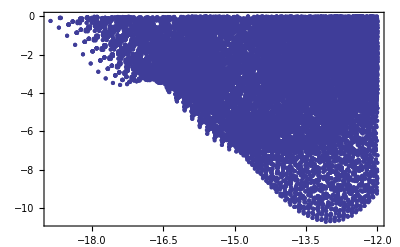
```mathematica
ComparisonPlot = -Graphics-
```

### Run GA

```mathematica
RealNDSGA[3,50,{-5,5},{f1,f2},200,BetaFactor->2,MutationRate->0.1,MutationSize->0.5]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]≥10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
Show[ComparisonPlot,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦All⟧,
PlotRange->{{-20,-14},{-12,1}},Frame->True,PlotStyle->(GrayLevel[1-#/Length[Generations]]&/@Range[Length[SelectedGenerations]])]]
```

```mathematica
CrowdingDistanceAssignment[SelectedGenerations⟦20⟧,{f1,f2}]/.{∞->1}
```

```mathematica
Sort[Transpose[{{f1[#],f2[#]}&/@SelectedGenerations⟦-1⟧,CrowdingDistanceAssignment[SelectedGenerations⟦-1⟧,{f1,f2}]/.{∞->1}}],#1⟦2⟧>#2⟦2⟧&]
```

```mathematica
Graphics[{GrayLevel[1-#⟦2⟧],Point[{f1[#⟦1⟧],f2[#⟦1⟧]}]}&/@Transpose[{#,CrowdingDistanceAssignment[#,{f1,f2}]/.{∞->1}}]&/@SelectedGenerations⟦-10;;-1⟧,Frame->True]
```